10

0.34

20

{3,5,3,1,1,2,2,3,3,2,2,4,7,3,1,2,4,6,1,3}

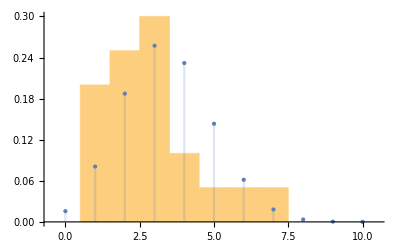

```mathematica
n = 10
p = .34
numflips =20
data = RandomVariate[BinomialDistribution[n,p],numflips]
Show[
Histogram[data,{-.5,n+.5,1},"PDF"],
DiscretePlot[PDF[BinomialDistribution[n,p],x],{x,0,n},PlotStyle-> PointSize[Large]]
]
```